#### Find all output files in current directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
filenames = FileNames["*.h5"];
```

Use one file a example

```mathematica
filename = filenames [[1]]
```

ResultBlackHole_N20_Nm2_K4_C1_DeltaN12_C00.01_Cm0.001_maxT20000_tol1e-06_samplingStep20_m40_Sim1.h5

#### Read out a parameter

```mathematica
K=Import[filename,{"Attributes","mode0"}][["K"]][[1]]
```

4

Total number of modes in specific model

```mathematica
nbModes = 2*K+2
```

10

#### Import and plot expectation values of modes

```mathematica
expectationValues = Table[Import[filename,ToString[StringForm["mode``",k]]],{k,0,nbModes-1}];
```

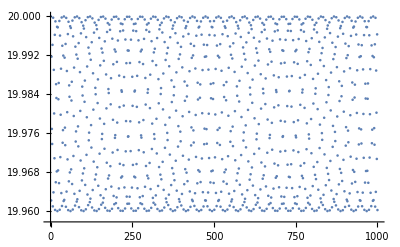
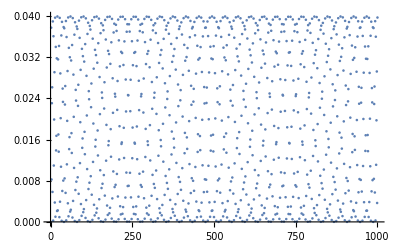
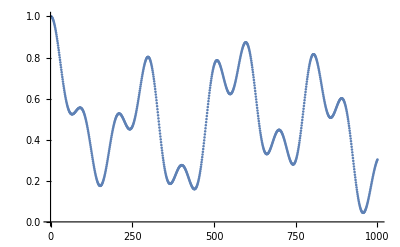
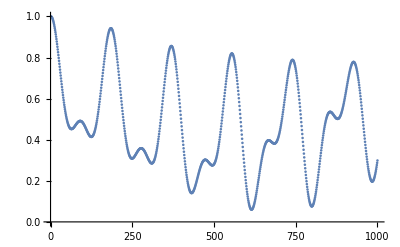
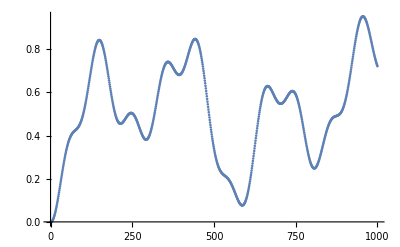
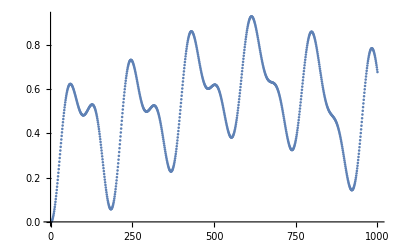
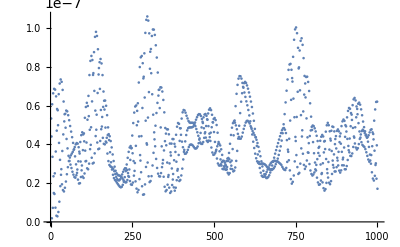
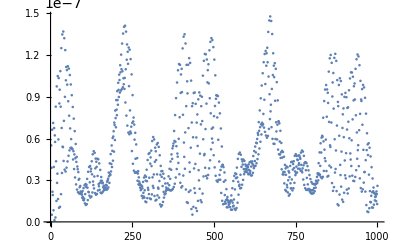

```mathematica
Map[ListPlot,expectationValues]
```